## Global Health DALYs

```mathematica
WHOraw=Import["C:\\Users\\Ben\\Documents\\wolfram\\Wolfram-Summer-School-2017-Project\\Data Sets\\GHE2015_DALYs-2015-country.csv"];
```

```mathematica
WHOheaders= Prepend[Last@DeleteCases[{ToString[WHOraw[[#,4]]],ToString[WHOraw[[#,5]]],ToString[WHOraw[[#,6]]],ToString[WHOraw[[#,7]]]},""]&/@Range[12,226],"Countries"];
```

```mathematica
WHOpopulation=WHOraw[[11,#]]&/@Range[8,190]
```

{32527,2897,39667,25022,92,43417,3018,23969,8545,9754,388,1377,160996,284,9496,11299,359,10880,775,10725,3810,2262,207848,423,7150,18106,11179,15578,23344,35940,521,4900,14037,17948,1383925,48229,788,4620,4808,22702,4240,11390,1165,10543,25155,77267,5669,888,10528,16144,91508,6127,845,5228,1313,99391,892,5503,64395,1725,1991,4000,80689,27410,10955,107,16343,12609,1844,767,10711,8075,9855,329,1311051,257564,79109,36423,4688,8064,59798,2793,126573,7595,17625,46050,112,3892,5940,6802,1971,5851,2135,4503,6278,2878,567,24235,17215,30331,364,17600,419,4068,1273,127017,104,2959,626,34378,27978,53897,2459,28514,16925,4529,6082,19899,182202,5211,4491,188925,3929,7619,6639,31377,100699,38612,10350,2235,50293,4069,19511,143457,11610,185,109,193,190,31540,15129,8851,96,6453,5604,5426,2068,584,10787,54490,12340,46122,20715,40235,543,1287,9779,8299,18502,8482,67959,2078,1185,7305,106,1360,11254,78666,5374,39032,44824,9157,64716,53470,321774,3432,29893,265,31108,93448,26832,16212,15603}

```mathematica
WHOfulldata=Join[{WHOraw[[8,#]]},WHOraw[[12;;226,#+6]]/WHOpopulation[[#-1]]]&/@Range[2,184]
```

{1}
 |  |  |  |

```mathematica
Export["C:/Users/Ben/Documents/WHOdata.mx",WHOfulldata]
```

C:/Users/Ben/Documents/WHOdata.mx

```mathematica
WHOcountryrules1=#1->StringReplace[#,{" and"," the",", The","-"," of","People's","Darussalam","n Federation","(Bolivarian Republic of)","(Plurinational State of)","(Islamic Republic of)","n Arab Republic","(Federated States of)","United Republic of","The former Yugoslav Republic of",", FYR",", RB",", Rep.","Gaza",", Fed. Sts."," SAR, China","America","n Arab Jamahiriya"," "}->""]&/@WHOfulldata[[2;;,1]];
```

```mathematica
WHOcountryrules2={"CaboVerde"->"CapeVerde","CÃ.b4ted'Ivoire"->"IvoryCoast","LaoDemocraticRepublic"->"Laos","Congo"->"RepublicCongo","Congo,Dem.Rep."->"DemocraticRepublicCongo","DemocraticRepublicKorea"->"NorthKorea","RepublicMoldova"->"Moldova","RepublicKorea"->"SouthKorea","VietNam"->"Vietnam","StatePalestine"->"WestBank","Egypt,ArabRep."->"Egypt","Iran,IslamicRep."->"Iran","LaoPDR"->"Laos","VirginIslands(U.S.)"->"UnitedStatesVirginIslands","SintMaarten(Dutchpart)"->"SintMaarten","SlovakRepublic"->"Slovakia","St.Martin(Frenchpart)"->"SaintMartin","KyrgyzRepublic"->"Kyrgyzstan","St.Lucia"->"SaintLucia","St.KittsNevis"->"SaintKittsNevis","St.VincentGrenadines"->"SaintVincentGrenadines","Korea,Dem.Peopleâ.80.99sRep."->"NorthKorea","Korea"->"SouthKorea","MacaoSAR,China"->"Macau","IsleMan"->"IsleOfMan"};
```

```mathematica
WHOdata=Join[{WHOheaders},Flatten[{Entity["Country",#[[1]]],#[[2;;]]}]&/@(WHOfulldata/.WHOcountryrules1)/.WHOcountryrules2[[2;;,All]]];
```

```mathematica
dataAssoWHO=AssociationThread[WHOheaders[[2;;]],Transpose[Map[Thread,MapThread[Rule,{WHOdata[[2;;,1]],WHOdata[[2;;,2;;]]}]]]];
```

```mathematica
dataAssoWHO=Map[Association,dataAssoWHO];
```

```mathematica
newDataAssoWHO=Map[Function[{propValues},Map[Association,GroupBy[Normal@propValues,countriesContinent[First@#]&]]],Map[Association,dataAssoWHO]];
```

### World Development Indicators

Import data from WDI spreadsheet

```mathematica
WDIraw=Import["C:\\Users\\Ben\\Documents\\wolfram\\Wolfram-Summer-School-2017-Project\\Data Sets\\WDIEXCEL.csv"];
```

```mathematica
WDIfulldata=Join[{WDIraw[[#,1]]},WDIraw[[#;;#+1503,58]]]&/@(Range[47,263]*1504+2);
```

Clean up country names so that Wolfram can interpret them as entities

```mathematica
Export["C:/Users/Ben/Documents/WDIdata.mx",WDIdataclean]
```

C:/Users/Ben/Documents/WDIdata.mx

```mathematica
WDIcountryrules1=#1->StringReplace[#,{" and"," the",", The","-"," of","People's","Darussalam","n Federation","(Bolivarian Republic of)","(Plurinational State of)","(Islamic Republic of)","n Arab Republic","(Federated States of)","United Republic of","The former Yugoslav Republic of",", FYR",", RB",", Rep.","Gaza",", Fed. Sts."," SAR, China"," "}->""]&/@WDIfulldata[[2;;,1]];
```

```mathematica
WDIcountryrules2={"CaboVerde"->"CapeVerde","Coted'Ivoire"->"IvoryCoast","LaoDemocraticRepublic"->"Laos","Congo"->"RepublicCongo","Congo,Dem.Rep."->"DemocraticRepublicCongo","DemocraticRepublicKorea"->"SouthKorea","RepublicMoldova"->"Moldova","RepublicKorea"->"NorthKorea","VietNam"->"Vietnam","StatePalestine"->"WestBank","Egypt,ArabRep."->"Egypt","Iran,IslamicRep."->"Iran","LaoPDR"->"Laos","VirginIslands(U.S.)"->"UnitedStatesVirginIslands","SintMaarten(Dutchpart)"->"SintMaarten","SlovakRepublic"->"Slovakia","St.Martin(Frenchpart)"->"SanMarino","KyrgyzRepublic"->"Kyrgyzstan","St.Lucia"->"SaintLucia","St.KittsNevis"->"SaintKittsNevis","St.VincentGrenadines"->"SaintVincentGrenadines","Korea,Dem.Peopleâ.80.99sRep."->"NorthKorea","Korea"->"SouthKorea","MacaoSAR,China"->"Macau","IsleMan"->"IsleOfMan","ChannelIslands"->"CookIslands"};
```

Process data so it is a matrix form with the first row of properties and the first column as country entities

```mathematica
WDIdata=Join[{Flatten[{"Countries",{WDIraw[[#,3]]}&/@Range[2,Length[WDIfulldata[[1]]]]}]},Replace[Flatten[{Entity["Country",#[[1]]],#[[2;;]]}]&/@((WDIfulldata/.WDIcountryrules1)/.WDIcountryrules2)[[2;;,All]],""->Missing[],{2}]];
```

Remove all property columns that have more than 100 data points missing

```mathematica
WDIdataclean=Transpose[Select[Transpose[WDIdata],Count[#,_Missing]<100&]]
```

{{Countries,Access to clean fuels and technologies for cooking  (% of population),Access to electricity (% of population),Access to electricity, rural (% of rural population),Access to electricity, urban (% of urban population),901,Urban population,Urban population (% of total),Urban population growth (annual %),Use of IMF credit (DOD, current US$)},215,{Zimbabwe,31.0993,36.4888,904,32.654,1.70815,519342000}}
 |  |  |  |

```mathematica
WDIdataPercent=Transpose[Prepend[DeleteCases[If[StringContainsQ[#[[1]],"%"], Flatten[Append[{},#]]]&/@Transpose[WDIdataclean],Missing[]],Transpose[WDIdataclean][[1]]]];
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Create a list of regions to be used in the visualization

```mathematica
continentCountries=AssociationMap[#["Entity"]&,{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant}];
```

```mathematica
countriesContinent=Association@Flatten[KeyValueMap[Function[{key,val},Map[(#->key)&, val ]],continentCountries],Infinity];
```

Process data so it is a series of associations from Property to Region to Country to Value

```mathematica
dataAsso=AssociationThread[WDIdataclean[[1,2;;]],Transpose[Map[Thread,MapThread[Rule,{WDIdataclean[[2;;,1]],WDIdataclean[[2;;,2;;]]}]]]];
```

```mathematica
dataAsso=Map[Association,dataAsso];
```

```mathematica
CityData[LinguisticAssistant,"Country"]
```

United Kingdom

```mathematica
newDataAsso=Map[Function[{propValues},Map[Association,GroupBy[Normal@propValues,countriesContinent[First@#]&]]],Map[Association,dataAsso]];
```

```mathematica
properties=Association[#[[1]]->#[[2;;]]&/@Transpose[WDIdataclean[[1;;,2;;]]]];
```

```mathematica
Manipulate[CorrelationTest[DeleteMissing[Transpose[{Rest[properties[Property1]],Rest[properties[Property2]]}],1,2]],{Property1,Keys@properties},{Property2,Keys@properties}]
```

Transpose::nmtx: The first two levels of {properties[],properties[]} cannot be transposed.

DeleteMissing::invrp: The argument Transpose[{properties[],properties[]}] is not a valid Association or a list.

CorrelationTest::invbvtd: The argument DeleteMissing[Transpose[{properties[],properties[]}],1,2] at position 1 should be a matrix of real numbers of dimension 2 with length greater than 2.

```mathematica
unitSplitStep[s_,del_,end_: "~~~Woo~~~"]:=Replace[StringSplit[s,del,2],{{_,u_}:>StringTrim@First@StringSplit[u,end],_->False}];
unitSplit[s_,reps:{__List}:{{"(",")"},{","}}]:=FirstCase[unitSplitStep[s,Sequence@@#]&/@reps,_String,s]
```

To see all the data at once, we can use a GeoRegionValuePlot with parameters of region and metric. The histogram allows us to understand the distribution across the selected region.

```mathematica
elements={1,2,4,6,34,52,96,229,230,245,254,257,267,271,280,339,345,355,379,387,390,394,455,456,500,508,651,652,737,781,902}
```

{1,2,4,6,34,52,96,229,230,245,254,257,267,271,280,339,345,355,379,387,390,394,455,456,500,508,651,652,737,781,902}

```mathematica
corrMat=Array[If[#1<=#2,Infinity,CorrelationTest[DeleteMissing[Transpose[{properties[[elements[[#1]]]],properties[[elements[[#2]]]]}],1,2]]]&,{Length[elements],Length[elements]}];
```

```mathematica
correlationPlot=MatrixPlot[corrMat,FrameTicks->{Transpose[{Range[Length[elements]],Keys@properties[[elements]]}],Map[{#[[1]],Rotate[#[[2]],π/2,{Left,0}]}&]@Transpose[{Range[Length[elements]],Keys@properties[[elements]]}]},PlotLegends->Automatic,
ImageSize->{Automatic,800}];
```

```mathematica
newDataAssoDalys = Dataset[<|"test"-> ""|>];
```

```mathematica
newDataAsso
```

<|Access to clean fuels and technologies for cooking  (% of population)→<|Europe→<|Albania→65.7515,Andorra→100,Austria→100,Belarus→99.9159,Belgium→100,Bosnia and Herzegovina→40.6094,Bulgaria→78.458,Croatia→93.6882,Cyprus→100,Czech Republic→99.99,Denmark→100,Estonia→91.0016,Faroe Islands→Missing[],Finland→100,France→100,Germany→100,Gibraltar→Missing[],Greece→100,Hungary→100,10,Malta→100,Moldova→92.7457,Monaco→100,Montenegro→73.5054,Netherlands→100,Norway→100,Poland→100,Portugal→100,Romania→81.2574,San Marino→Missing[],Serbia→70.6804,Slovakia→99.99,Slovenia→97.5221,Spain→100,Sweden→100,Switzerland→100,Ukraine→97.0215,United Kingdom→100|>,6,1→1|>,907,1|>
 |  |  |  |

```mathematica
newDataAssoWHO
```

<|All Causes→<|Asia→<|Afghanistan→0.59438,Armenia→0.321471,Azerbaijan→0.315583,Bahrain→0.169499,Bangladesh→0.302093,Bhutan→0.357032,Brunei→0.181324,Cambodia→0.338002,China→0.262129,28,Syria→0.475976,Tajikistan→0.336949,Thailand→0.326026,Turkey→0.262947,Turkmenistan→0.39118,United Arab Emirates→0.162226,Uzbekistan→0.330489,Vietnam→0.267128,Yemen→0.400626|>,5,1|>,213,1|>
 |  |  |  |

```mathematica
GeoRegionValuePlot[Flatten@Normal@Values@(datasetList[[2]][First@Keys@(datasetList[[2]])])]
```

-Graphics-

```mathematica
datasetList={newDataAsso,newDataAssoWHO,newDataAssoDalys};
```

```mathematica
DynamicModule[
	{Property2 = Keys[(datasetList[[1]])]⟦2⟧, data=Flatten@Normal@Values@(datasetList[[1]][First@Keys@(datasetList[[1]])]),data2=Flatten@Normal@Values@(datasetList[[1]][First@Keys@(datasetList[[1]])]),
	Data=1, Graphic=1, Property=First@Keys@(datasetList[[1]]), Region = EntityClass["Country","Countries"],init=False,display},
Panel@Column[{
	SetterBar[Dynamic[Data],{1->"    Development Indicators   ",2->"    Health DALYS    ",3->"   NGO Distribution    "}],
	SetterBar[Dynamic[Graphic],{1->"   Distribution Map   ",2->"      Chart      ",3->"   Correlation Graph   "}],
	Dynamic[If[!MemberQ[Keys[datasetList⟦Data⟧], Property], Property=First@Keys[datasetList⟦Data⟧]];
	PopupMenu[Dynamic[Property],Keys@(datasetList[[Data]])]],
	PopupMenu[Dynamic[Region],
		{EntityClass["Country","Europe"],EntityClass["Country","SouthAmerica"],EntityClass["Country","NorthAmerica"],EntityClass["Country","Oceania"],EntityClass["Country","Asia"],EntityClass["Country","Africa"],LinguisticAssistant}
	],
	DynamicWrapper[
		PaneSelector[{
	   1 -> 		
		PaneSelector[{
			True -> Labeled[
			Dynamic[GeoRegionValuePlot[
			data,GeoLabels->(Tooltip[#1,#2->#4]&),PlotLegends->False, GeoBackground->GeoStyling["ReliefMap"],MissingStyle->White,PlotLabel-> "Distribution Map",ImageSize->{Automatic,300}
			], TrackedSymbols:>{data}],
			Labeled[
				Dynamic[SmoothHistogram[DeleteMissing@Values@data,
				ColorFunction->(ColorData["GeographyGradient"][#]&),
				Filling->Axis,
				Axes->{True,False}, 
				PlotRange->All
			], TrackedSymbols:>{data}], Dynamic@unitSplit@Property,Bottom],Right
		],
		False -> Plot[x^2,{x,1,4}]
		}, Dynamic[Data < 3]],
		2 ->
			Dynamic[BarChart[DeleteMissing[Values@SortBy[data,Values]][[-10;;]],ChartLabels->Placed[Keys@DeleteMissing[SortBy[data,Values]][[-10;;]],After],ColorFunction->"Rainbow",BarOrigin->Left,ImageSize->{Automatic,500}]],

		3 ->
		Dynamic[If[!MemberQ[Keys@(datasetList[[Data]]),Property2],Property2=Keys[(datasetList[[Data]])]⟦2⟧];
			Column[{
			Dynamic[
			 PopupMenu[Dynamic[Property2],Keys@(datasetList[[Data]])]],
			CorrelationTest[DeleteMissing[Transpose[{Rest[Values@data],Rest[Values@data2]}],1,2]],correlationPlot
		}]]
	},
	Dynamic[Graphic],
	ImageSize->Automatic
	],
	{data=
		If[Region===EntityClass["Country","Countries"],
			Flatten@Normal@Values@(datasetList[[Data]][Property]),
			Normal@(datasetList[[Data]][Property][Region])],
		If[!MemberQ[Keys@(datasetList[[Data]]),Property2],
			Property2=Keys[(datasetList[[Data]])]⟦2⟧];
			,
	data2=
		If[Region===EntityClass["Country","Countries"],
			Flatten@Normal@Values@(datasetList[[Data]][Property2]),
			Normal@(datasetList[[Data]][Property2][Region])]},
		
		
	SynchronousUpdating -> False]}
	]
	
	
]
```

```mathematica
DynamicModule[{Property2=Keys[(datasetList[[1]])][[2]],data,data2,Data=1,Graphic=1,Property=First@Keys@(datasetList[[1]]),Region=EntityClass["Country","Countries"]},Panel@Column[{SetterBar[Dynamic[Data],{1->"    Development Indicators   ",2->"    Health DALYS    ",3->"   NGO Distribution    "}],SetterBar[Dynamic[Graphic],{1->"   Distribution Map   ",2->"      Chart      ",3->"   Correlation Graph   "}],Dynamic[If[!MemberQ[Keys[datasetList[[Data]]],Property],Property=First@Keys[datasetList[[Data]]]];PopupMenu[Dynamic[Property],Keys@(datasetList[[Data]])]],PopupMenu[Dynamic[Region],{EntityClass["Country","Europe"],EntityClass["Country","SouthAmerica"],EntityClass["Country","NorthAmerica"],EntityClass["Country","Oceania"],EntityClass["Country","Asia"],EntityClass["Country","Africa"],LinguisticAssistant}],DynamicWrapper[PaneSelector[{1->PaneSelector[{True->Labeled[Dynamic[GeoRegionValuePlot[data,GeoLabels->(Tooltip[#1,#2->#4]&),PlotLegends->False,GeoBackground->GeoStyling["ReliefMap"],MissingStyle->White,PlotLabel->"Distribution Map",ImageSize->{Automatic,300}],TrackedSymbols:>{data}],Labeled[Dynamic[SmoothHistogram[DeleteMissing@Values@data,ColorFunction->(ColorData["GeographyGradient"][#]&),Filling->Axis,Axes->{True,False},PlotRange->All],TrackedSymbols:>{data}],Dynamic@unitSplit@Property,Bottom],Right],False->Plot[x^2,{x,1,4}]},Dynamic[Data<3]],2->Dynamic[BarChart[Values@SortBy[data,Values][[-10;;]],ChartLabels->Placed[Keys@SortBy[data,Values][[-10;;]],After],ColorFunction->"Rainbow",BarOrigin->Left,ImageSize->{Automatic,500}]],3->Dynamic[Column[{Dynamic[PopupMenu[Dynamic[Property2],Keys@(datasetList[[Data]])]],CorrelationTest[DeleteMissing[Transpose[{Rest[Values@data],Rest[Values@Flatten@Normal@Values@(datasetList[[Data]][Property2])]}],1,2]],correlationPlot}]]},Dynamic[Graphic],ImageSize->Automatic],{data=If[Region===EntityClass["Country","Countries"],Flatten@Normal@Values@(datasetList[[Data]][Property]),Normal@(datasetList[[Data]][Property][Region])],If[!MemberQ[Keys@(datasetList[[Data]]),Property2],Property2=Keys[(datasetList[[Data]])]⟦2⟧];,data2=If[Region===EntityClass["Country","Countries"],Flatten@Normal@Values@(datasetList[[Data]][Property2]),Normal@(datasetList[[Data]][Property2][Region])]},SynchronousUpdating->False]}]]
```

```mathematica
DynamicModule[{init=False,display},
Dynamic[If[!init,ProgressIndicator[Appearance->"Necklace"],display]],
Initialization:>(init=False;Pause[5];display=1;init=True),
SynchronousInitialization->False
]
```

```mathematica
GeoRegionValuePlot[Normal@(newDataAsso["Access to clean fuels and technologies for cooking  (% of population)"][EntityClass["Country","SouthAmerica"]]),GeoLabels->(Tooltip[#1,#2->#4]&)			]
```

```mathematica
Manipulate[
	With[
	{
	data=
	If[Region===LinguisticAssistant,
		Flatten@Normal@Values@(datasetList[[Data]][Property]),
		Normal@(datasetList[[Data]][Property][Region])
	]
	},
	
	Which[
		Data<3&&Graphic===1,
			
		Labeled[
			GeoRegionValuePlot[data,MissingStyle->White,PlotLabel-> "Distribution Map",GeoLabels->(Tooltip[#1,#2->#4]&),
			PlotLegends->False,GeoBackground->GeoStyling["ReliefMap"]],
			Labeled[
				SmoothHistogram[DeleteMissing@Values@data,
				ColorFunction->(ColorData["GeographyGradient"][#]&),
				Filling->Axis,
				Axes->{True,False}, 
				PlotRange->All
			],
			unitSplit@Property,Bottom],Right],

		Graphic===2, 
				BarChart[DeleteMissing[Values@SortBy[data,Values]][[;;10]],ChartLabels->Placed[Keys@SortBy[data,Values][[;;10]],After],ColorFunction->"Rainbow",BarOrigin->Left,PlotLabel->"Top 10 Countries"],
		Graphic===3,
				correlationPlot
		]
	],
{{Data,1},{1->"    Development Indicators   ",2->"    Health DALYS    ",3->"   NGO Distribution    "},ControlType->SetterBar},{{Graphic,1},{1->"   Distribution Map   ",2->"      Chart      ",3->"   Correlation Graph   "}},
{{Property,First@Keys@(datasetList[[1]])},Keys[datasetList[[Data]]],ControlType->PopupMenu},{{Region,EntityClass["Country","Countries"]},{LinguisticAssistant,EntityClass["Country","Europe"],EntityClass["Country","SouthAmerica"],EntityClass["Country","NorthAmerica"],EntityClass["Country","Oceania"],EntityClass["Country","Asia"],EntityClass["Country","Africa"]}}
]
```

Part::partd: Part specification datasetList⟦1⟧ is longer than depth of object.

Keys::invrl: The argument datasetList⟦1⟧ is not a valid Association or a list of rules.

```mathematica
Values@SortBy[Flatten@Normal@Values@(datasetList[[1]]["Access to clean fuels and technologies for cooking  (% of population)"]),Values][[10;;]]
```

{2.0239,2.6778,2.79523,2.79942,2.84854,3.06854,3.38511,3.44176,3.67084,3.93876,4.21324,4.4492,5.38655,5.68418,5.74153,6.00041,6.24071,6.40164,6.44002,6.71621,8.37454,8.48086,8.75798,8.76983,9.35358,10.1747,12.8197,13.0823,15.8633,15.8812,17.173,17.3589,18.4798,19.3947,19.7318,21.0003,21.6942,24.1903,24.7552,27.3495,29.2546,29.5506,30.0433,30.917,31.0993,31.6207,33.4998,34.7347,36.0769,36.1768,36.4378,40.6094,40.6804,43.3714,43.8115,44.4435,45.1258,45.5808,47.1899,48.2025,48.9816,52.3721,54.7612,56.4508,58.0837,59.9602,61.3488,61.4306,62.0969,62.2236,62.5763,65.5151,65.7515,65.9304,69.9614,70.6804,71.0556,71.7506,73.5054,74.775,75.3622,78.1725,78.458,80.0346,81.0731,81.2574,85.3252,85.9113,85.9232,86.6923,89.6167,90.0392,90.2148,91.0016,91.1079,91.1937,91.256,91.7796,92.6971,92.7457,93.6882,95.1913,95.3113,95.89,96.6901,96.8509,97.0215,97.1326,97.2992,97.5221,98.0986,98.7183,98.863,98.8772,99.5279,99.6114,99.6688,99.6956,99.8326,99.869,99.8727,99.9159,99.9163,99.9788,99.9833,99.9852,99.9873,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,99.99,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]}

```mathematica
7
```

7

```mathematica
First@Keys[datasetList[[1]]]
```

Access to clean fuels and technologies for cooking  (% of population)

```mathematica
newDataAsso[[1]];
```

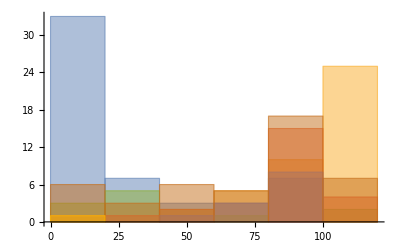

```mathematica
Histogram[newDataAsso[[1]]]
```

```mathematica
GeoRegionValuePlot[{LinguisticAssistant->"a",LinguisticAssistant->"b",LinguisticAssistant->"c"}]
```

-Graphics-

```mathematica
DynamicModule[{x,1,2},GeoRegionValuePlot[{LinguisticAssistant->x,LinguisticAssistant->3*x}]]
```

DynamicModule::lvsym: Local variable specification {x,1,2} contains 1, which is not a symbol or an assignment to a symbol.

DynamicModule::lvsym: Local variable specification {x,1,2} contains 2, which is not a symbol or an assignment to a symbol.

DynamicModule[{x,1,2},GeoRegionValuePlot[{Laos→x,Vietnam→3 x}]]